```mathematica
(*
Code by Junyu Liu, junyu@mail.ustc.edu.cn;
The following code produces the functions grf[point,horizontal scale, vertical scale] and grfreset.
grf[point,horizontal scale, vertical scale] takes the set point, the scales and the variables inval and inpoints to produce a Gaussian random field of Gaussian covariance at the point. If applicable, it appends the obtained value to the variables inpoints and inval that contain the already evaluated GRF.
grfreset[] is used to reset the variables inpoints and inval to obtain a new GRF.

EXAMPLE: grf[{0,0,0},1,1] produces the GRF value at the point {0,0,0} with unit scales.
grfreset[]; resets the GRF.
*)

(*REAL GRF*)
distribution=TransformedDistribution[r Exp[0*I t],{r\[Distributed]NormalDistribution[0 ,1],t\[Distributed]UniformDistribution[{0,2 Pi}]}]; (*Define distribution to draw GRF from*)

(*(*CMPLX GRF*)
distribution=TransformedDistribution[r Exp[I t],{r\[Distributed]NormalDistribution[0 ,1],t\[Distributed]UniformDistribution[{0,2 Pi}]}]; (*Define distribution to draw GRF from*)*)



grfreset:=Module[{},inpoints={};
inval={};
];(*Resets internal cache that stores data points: variables are inval, inpoints*)

corr[x_]=Exp[-x^2];(*Define correlation function: here it's Gaussian*)

(*Define main function that produces GRF: grf[point,horizontal scale, vertical scale] gives GRF value constructed from inpoints, inval variables corresponding to specified scales. Variables inpoints and inval are of unit scale.*)
grf[newpoint_,lh2_,lv2_]:=Module[{val},
dim=Length[newpoint];
lh=lh2; (*Horizontal scale*)
lv=lh2; (*Vertical scale*)
val=lv*evaluateat[newpoint*1/lh];val];


(*evaluateat checks if specified point already exists in inpoints, otherwise it calls grfadd which generates the GRF at the specified point. If applicable (i.e. if point is reliable), it is appended to the variables inpoints and inval*)
evaluateat[newpoint_]:=Module[{len,val,check},
{len=Length[inpoints];
If[len==0,{
inpoints={newpoint};
val=RandomVariate[distribution];
inval={val};},

{check=Position[inpoints,newpoint];

If[Length[check]==0,
val=grfadd[newpoint];
If[checkit==0,
{inval=Append[inval,val];
inpoints=Append[inpoints,newpoint];}
];,
{
val=inval[[check[[1,1]]]];}
];
}];
val}
][[1]];


(*grfadd produces the GRF at the specified point. It also sets the variable checkit that indicates if the new point is reliable, i.e. if the error on the new point is small enough to be trusted.*)
grfadd[newpoint_]:=Module[{len},
len=Length[inpoints];
c0=1;
normm=Sqrt[Total[Abs[Transpose[Transpose[inpoints]-newpoint]]^2,{2}]];
boole=Boole[Negative[normm-5]];(*selects all points from inpoints that are within 5 correlation lengths of the newpoint*)
sel=Flatten[Position[boole,1]];
sellen=Length[sel];

	If[sellen==0,
		{a=RandomVariate[distribution]},
		{invalsel=Table[inval[[ii]],{ii,sel}];
		inpointssel=Table[inpoints[[ii]],{ii,sel}];
		m3=Table[0,{sellen},{sellen}];
		Table[{inplast=inpointssel[[i]] ;
			normm2=Sqrt[Total[Abs[Transpose[Transpose[Take[inpointssel,i]]-inplast]]^2,{2}]];
			normm2=Take[normm2,i-1];
			m3[[i,1;;i-1]]=normm2;
			m3[[1;;i-1,i]]=normm2;
			}
		,{i,2,sellen}];
		csel=corr[m3];
		cjsel=corr[normm[[sel]]];
		fasel=Quiet[LinearSolve[csel,cjsel]];
		fa22sel=1-cjsel.fasel;
		fa2sel=Sqrt[fa22sel];		
		pre=Norm[csel.fasel-cjsel];
		If[Or[pre>10^-12,fa22sel/Norm[fasel]<10^-6],
		{checkit=1;
			fa2sel=0;},checkit=0
		];
a=fa2sel*RandomVariate[distribution]+fasel.invalsel;
}
];
a
];
```

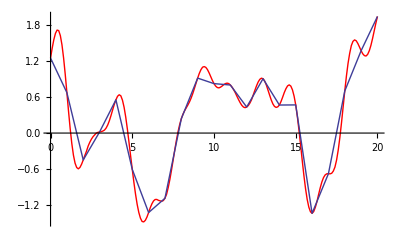

```mathematica
(*EXAMPLES*)
(*1D*)
grfreset[];datcoarse=Table[{x,grf[{x},1.,1.]},{x,0,20,1}];datfine=Table[{x,grf[{x},1.,1.]},{x,0,20,.1}];Show[ListPlot[datfine,Joined->True,PlotStyle->Red],ListPlot[datcoarse,Joined->True]]
```

```mathematica
(*2D example*)
```

```mathematica
grfreset[];n=100;datcoarse=ConstantArray[0,{n+1,n+1}];plots=Table[{},{300}];

For[i=1,i<200,i++,{pos1=1+Round[{n/2-Sin[π/2 i/100]n/2,n/2-Cos[π/2 i/100]n/2}];pos2=1+Round[{n/2+Sin[π/2 i/100]n/2,n/2-Cos[π/2 i/100]n/2}];datcoarse[[pos1[[1]],pos1[[2]]]]=grf[(pos1-1)/n,.2,.2];datcoarse[[pos2[[1]],pos2[[2]]]]=grf[(pos2-1)/n,.2,.2];plots[[i]]=MatrixPlot[datcoarse,PlotRange->{-4,4}];}];
For[i=1,i<100,i++,{pos1=1+Round[{n/2,n -n i/100}];datcoarse[[pos1[[1]],pos1[[2]]]]=grf[(pos1-1)/n,.2,.2];plots[[i+200]]=MatrixPlot[datcoarse,PlotRange->{-4,4}];}];

Animate[plots[[ii]],{ii,1,300,1}]
```